## Simple Error Analysis

### Declaring quantities with error (Around and MeanAround)

We can declare a quantity which has a built in error using Around[μ,σ]. This represents a random variable being pulled from a normal distribution where μ is the mean of the distribution and σ is the standard deviation. I’ll explain more about what this means in the following sections.

```mathematica
a = Around[3,0.1]
```

3.000.10

What if we want to find the mean of a list of data? Sure, we could just call Mean on the list of data. But this will only give us the mean and tell us nothing about the variance of our list. So instead, it’s much better to store the result as an Around property. Which we can do in two ways as we’ll see below.

Sometimes stats can be a bit confusing tho, so let’s think about this from the perspective of a toy example. Lets say we have some list of measurements for instance from some noisy probe, and we want to know the mean value the probe was measuring. We can do this in the following ways:

```mathematica
Measurements ={1.39,1.45,0.07,-0.22,0.55,0.19,2.28,0.65,0.70,1.28,1.11,0.65,0.71,1.54,0.83,1.45,0.51,1.92,1.42,0.25};

x̄=Mean[Measurements];
σ = StandardDeviation[Measurements];
n=Length[Measurements];
Subscript[σ, x̄] =σ/(√n);

AvgMeasurement= Around[x̄,Subscript[σ, x̄]]

AvgMeasurement2=MeanAround[Measurements]
```

0.940.14

0.940.14

### What does this actually mean?

When we define a value with error using either Around or MeanAround, it represents a parameter we only know within some certainty. The assumption is that this variable (μ±σ) will be Normally distributed with mean of μ and a standard deviation of σ. In the case of MeanAround, this will always be true if you have enough samples in your list for the central limit theorem to apply, and the distribution at hand is the distribution of sample means associated with your dataset.

### Error propagation

Because we assume these Around values are normally distributed, we can use gaussian error propagation formulas to find the error of derived quantities. You may remember having to do this by hand using the following formulas in intro physics lab for instance. 
-Graphics-
You may also remember from intro physics lab, that doing this by hand is a huge pain. Thankfully, Mathematica will just do it for you. And ofc it can even do it symbolically.

```mathematica
ClearAll[x,y,μx,μy,σx,σy]
x = Around[μx,σx];
y = Around[μy,σy];

x+y
x-y
x y
x/y
```

μx+μy√(σx^2+σy^2)

μx-μy√(σx^2+σy^2)

μx μy√(μy^2 σx^2+μx^2 σy^2)

μx/μy√(σx^2/μy^2+μx^2 Abs[σy/μy^2]^2)

So for-instance, let’s say we had two sets of data. One pertaining to the measured speed of a car, and the other to the time it took this car to go down a certain track, we could estimate the length of the track and know how uncertain we are in the accuracy of our measurement. Which is obviously crucial as engineers.

```mathematica
RaceTimes = {10.951371129369143,10.969585854558085,10.138424635516337,10.431830899681664,11.630490028139766,10.073977993782517,9.53016757468714,9.267948250418083,10.973895821874223,11.443449756825887,9.892721449616635,10.999728654672234,10.388198279379456,9.582547165913827,7.579279662904378,10.849437868790087,11.743322636181974,10.267395546552525,9.394374627977776,10.149102132348794,9.422969437264346,10.859249887898962,10.258064420029969,10.595187478157726,10.028425079585013,10.23787768301899,9.720135628790016,9.130047464573574,10.224189334361476,11.009569252061898};
CarSpeeds = {62.42111973276015,59.15143081424588,64.42360676023429,64.22921681398381,63.06512374703491,61.00491854636967,65.38855270478581,58.40216646385667,67.4244853925836,59.406769092663126,60.05015613619699,58.70295859338827,63.77613520385608,64.05486958063442,60.793151709860624,61.749559351155725,64.92679175763878,59.81816396399934,58.03743680927357,61.74437005702066,59.54301091704348,58.740275108363704,58.53622320229351,63.39745866237974,58.511039580035224,62.0906719385223,59.44669127269559,62.28635500994682,59.86051611677373,61.76058232540365};

t = MeanAround[RaceTimes]
v = MeanAround[CarSpeeds]

d = v t
```

10.260.16

61.40.5

630.11.

Oh yeah, and ofc Mathematica can deal with units and error for you at the same time without even breaking a sweat.

```mathematica
RaceTimes = Quantity[{10.951371129369143,10.969585854558085,10.138424635516337,10.431830899681664,11.630490028139766,10.073977993782517,9.53016757468714,9.267948250418083,10.973895821874223,11.443449756825887,9.892721449616635,10.999728654672234,10.388198279379456,9.582547165913827,7.579279662904378,10.849437868790087,11.743322636181974,10.267395546552525,9.394374627977776,10.149102132348794,9.422969437264346,10.859249887898962,10.258064420029969,10.595187478157726,10.028425079585013,10.23787768301899,9.720135628790016,9.130047464573574,10.224189334361476,11.009569252061898},"Minutes"];
CarSpeeds = Quantity[{62.42111973276015,59.15143081424588,64.42360676023429,64.22921681398381,63.06512374703491,61.00491854636967,65.38855270478581,58.40216646385667,67.4244853925836,59.406769092663126,60.05015613619699,58.70295859338827,63.77613520385608,64.05486958063442,60.793151709860624,61.749559351155725,64.92679175763878,59.81816396399934,58.03743680927357,61.74437005702066,59.54301091704348,58.740275108363704,58.53622320229351,63.39745866237974,58.511039580035224,62.0906719385223,59.44669127269559,62.28635500994682,59.86051611677373,61.76058232540365},("Miles")/("Hours")];

t = MeanAround[RaceTimes]
v = MeanAround[CarSpeeds]

d =UnitConvert[ v t,"Kilometers"]
```

(10.260.16) min

(61.40.5) mi/h

(16.900.29) km

Essentially, what this is telling us, is that if we repeated this experient a bunch of times, and plotted a histogram of the track distances we computed (using samples of the same size each time). We would expect them to form a normal distribution centered at 16.9km with a standard deviation of 0.29km. As such, this means we can be 68.3% sure that the true value for the tack distance lies inside of the (16.900.29) "km" prediction range.
-Graphics-

### Grabbing values from Around quantities

Sometimes it’s useful to grab just the value or uncertainty of one of these variables with error. And this is also very easy to do as follows

```mathematica
x= Around[10,2]
x["Value"]
x["Uncertainty"]
```

10.02.0

10.

2.

Mathematica stores these values as properties of the quantity, similarly to how we grab properties from regression models in week 5. And just like we did for regression models we can also see the other properties we can grab from these quantities

```mathematica
x["Properties"]
```

{Number,Distribution,Interval,Uncertainty,Value}

```mathematica
x["Distribution"]
x["Interval"]
x["Number"]
```

NormalDistribution[10.,2.]

Interval[{8.,12.}]

10.

However sometimes there is a slight problem, for-instance lets see what happens when we try to grab the value of d from the above example.

```mathematica
d = Quantity[(16.900.29), "Kilometers"]
d["Value"]
d["Uncertainty"]
```

(16.900.29) km

((16.900.29) km)[Value]

((16.900.29) km)[Uncertainty]

It doesn’t work? Why? 

Well, here’s what Mathematica actually sees:

```mathematica
Quantity[Around[16.90,0.29],"Kilometers"]["Value"]
```

((16.900.29) km)[Value]

So we’re trying to grab the value of a Quantity not Around, and Quantity doesn’t have a property named “Value”. We can easily fix this with a simple replacement rule instead though as follows:

```mathematica
d = Quantity[(16.900.29), "Kilometers"]
d/.a_Around:>a["Value"]
d/.a_Around:>a["Uncertainty"]
```

(16.900.29) km

16.9008 km

0.28677 km

Instead of just trying to take the value of d, we’re replacing anything with a Head of Around with its value.

### Intervals and worst-case predictions

You may have noticed that when we use gaussian error propagation, the total error of the output is always less than what you would get if you individually put both the upper and lower bound through a calculation. For instance:

```mathematica
a = Around[5,1];
b = Around[4,3];
(5-1)(4-3)
(a b)
(5+1)(4+3)
```

4

20.16.

42

This works because of the assumption that our error is gaussian. If we don’t know this to be true, however, we can instead just find the minimum and maximum range like we did above. But ofc, Mathematica also has a way to do this for us and it’s using intervals instead of around quantities.

```mathematica
a=Interval[{5-1,5+1}];
b=Interval[{4-3,4+3}];
a b
```

Interval[{4,42}]

Alternatively for we can also get intervals from Around like we saw above

```mathematica
a = Around[5,1]["Interval"];
b = Around[4,3]["Interval"];
a b
```

Interval[{4.,42.}]

In cases where you don’t have reason to believe your error is gaussian, or where you want to find a very conservative error estimate, this is the safest bet. Although it is important to note that all this tells you is that the most likely true answer lies somewhere in that interval, but it gives you no information about where in that interval you are most likely to find the answer. Here the center of the interval is not always the most likely place you’d find the answer!

## Propagating Error Through Functions

### What does this even mean?

Before when we were using simple error propagation formulas for the addition or multiplication of quantities with error, we didn’t have any issues because when you add two gaussian distributed random variable you get another gaussian. And when you divide them you get something which is approximately normal-ish looking, but technically follows a different distribution. The same is true for multiplication. Nevertheless though, the variances of these resulting distributions are correctly predicted by the error propagation formulas. For instance, let’s look at an example:

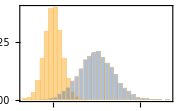
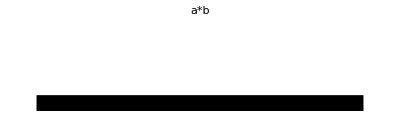
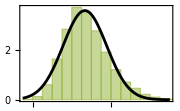

Predicted c = 0.670.11
True      c = 0.680.12

```mathematica
(* Define some variables with error *)
a= Around[10,1];
b=Around[15,2];
(* Simulate the process of taking 10,000 measuurments from each of their distributions *)
SeedRandom[12341];
aSample = RandomVariate[a["Distribution"],10000];
bSample = RandomVariate[b["Distribution"],10000];
(* Next compute their product and also simulate the process of sampling their ratios *)
c = a/b;
cSample = RandomVariate[a["Distribution"],10000]/RandomVariate[b["Distribution"],10000];
(* Now lets compare the true ratio distribution to the one we get by just propagating the error *)

Row[{
Histogram[{aSample,bSample},Automatic,"PDF",ChartLegends->{"a","b"},Frame->True,ImageSize->Small],
Graphics[{Arrowheads[0.25],Thickness[0.05],Arrow[{{0,0},{1,0}}],Text[Style["a*b",Large],{0.5,0.3}]}],
Show[{
Histogram[cSample,Automatic,"PDF",Frame->True,ChartStyle->Directive[ColorData[97,3],Opacity[0.5]],ChartLegends->{"True c"}],
Plot[PDF[c["Distribution"],cc],{cc,0.35,1.1},PlotLegends->{"Aproximated c"},PlotStyle->Black]
},ImageSize->Small]
}]
Column[{
Row[{"Predicted c = ",c}],
Row[{"True      c = ",Around[Mean[cSample],StandardDeviation[cSample]]}]
}]
```

So we can see that even though dividing two gaussians doesn’t actually result in another gaussian for instance, it looks close enough in most cases that it doesn’t matter toooo much for simple operations like this. But what if we try to propagate our error through a more complicated function? Like e^x for instance? It’s not possible to have an arbitrary formula for propagating error through any function, and yet Mathematica gives us an answer when we ask it to do this.

```mathematica
a = Around[10,0.01];
f[x_]:=ⅇ^x;
f[a]
```

22026.220.

But what is Mathematica doing? It’s treating e^x as a simple linear function obtained using Taylor expansion and using standard error propagation through this linear function. Lets see why this works: 

	f(x ± Δx) =  ∑_(n=0)^∞ (f^(n)(x))/(n!)(±Δx)^n
⇒	f(x ± Δx) ≈	 f(x) ± f’(x)Δx + O(Δx^2)

Let’s try this for ourself:

```mathematica
a = Around[10,0.01];
f[x_]:=ⅇ^x;
f[a]
Around[f[a["Value"]],f'[a["Value"]]*a["Uncertainty"]]
```

22026.220.

22026.220.

And look at that! We get the same result. But is this result even right? Well, the error in this prediction scales with the square of the uncertainty as shown by the O(Δx^2) term in the series above. And so for values with small errors or functions which are somewhat linear, this approximation holds just fine. But when either of these assumptions break down, the prediction gets much worse.  

It is also worth noting that a more general version of this same formula can be written for multi-variable functions as follows:  
f(x⃗ ± OverVector[Δx] ) ≈ f(x⃗) ± ∇f · OverVector[Δx] 

And this is exactly what Mathematica uses for such cases. However, it is very important to note that this can give you very bad results in many cases, especially when the resulting distribution isn’t gaussian.  Let’s take a look at an example like this:

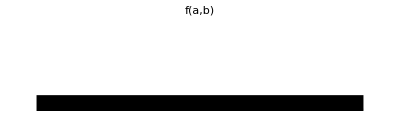
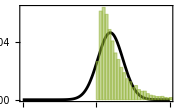
-Graphics--Graphics--Graphics-

Predicted c = 95.85.
True      c = 133.129.

```mathematica
(* Define our new complicated function *)
f[a_,b_]:= 1/10^12(a+b)^10;
(*Define some variables with error*)
a= Around[10,1];
b=Around[15,2];
(* Simulate the process of taking 10,000 measuurments from each of their distributions *)
SeedRandom[12341];
aSample = RandomVariate[a["Distribution"],10000];
bSample = RandomVariate[b["Distribution"],10000];
(* Next apply the function to the samples *)
c = f[a,b];
cSample = f[aSample,bSample];
(* Now lets compare the true product distribution to the one we get by just propagating the error *)
Row[{
Histogram[{aSample,bSample},Automatic,"PDF",ChartLegends->{"a","b"},Frame->True,ImageSize->Small],
Graphics[{Arrowheads[0.25],Thickness[0.05],Arrow[{{0,0},{1,0}}],Text[Style["f(a,b)",Large],{0.5,0.3}]}],
Show[{
Plot[PDF[c["Distribution"],cc],{cc,-500,500},PlotLegends->{"Aproximated c"},PlotStyle->Black,Frame->True],
Histogram[cSample,Automatic,"PDF",Frame->True,ChartStyle->Directive[ColorData[97,3],Opacity[0.5]],ChartLegends->{"True c"}]
},ImageSize->Small,PlotRange->{{-500,500},All},Axes->False]
}]
Column[{
Row[{"Predicted c = ",c}],
Row[{"True      c = ",Around[Mean[cSample],StandardDeviation[cSample]]}]
}]
```

Oh.... uhhhh ok... Not so great. Why? 

Well, the assumption that gaussian error propagation should hold for this function is completely out the window. I mean, why would it? There’s no reason to expect it to. As we can see the gaussian will have non-zero probability at negative values but this function can never return a negative and so by that alone we know the result can’t be gaussian.

### Higher order error propagation and AroundReplace

So, can we do any better? Well, what if we were to use a higher order Taylor Series approximation for the function instead of just a first order? In that case, it is possible to derive a formula  for arbitrary high orders using probability theory. However, the formulas get really messy really fast. As such, Mathematica currently only supports up to 4th order approximations through the function AroundReplace. 

Let’s take a look at the same example from above.

```mathematica
(* True value of c*)
Around[Mean[cSample],StandardDeviation[cSample]]
(* First order prediction *)
f[a,b]
(* Second order prediction *)
AroundReplace[f[aa,bb],{aa->a,bb->b},2]
(* Third order prediction *)
AroundReplace[f[aa,bb],{aa->a,bb->b},3]
(* Fourth order prediction *)
AroundReplace[f[aa,bb],{aa->a,bb->b},4]
```

133.129.

95.85.

130.98.

130.122.

134.127.

We can see that as we increase the series order the predicted values get much closer to the ones we computed directly by taking tons of random samples.